## Measuring Customer Satisfaction

Based on a March 2016 McKinsey Quarterly article, “From Touchpoints to Journeys: Seeing the World as Customers Do” by Nicolas Maechler, Kevin Neher, and Robert Park. 

Customer satisfaction is tracked by looking at customer touch points -- the points where the customer interacts with the company supplying the product or service. For each touch point, a company usually sets up a process for interacting with the customer and measuring customer satisfaction at that touchpoint.

“Consider the dilemma that executives faced at one media company. Customers were leaving at an alarming rate, few new ones were available for acquiring in its market, and even the company’s best customers were getting more expensive to retain.

...While the company’s overall customer-satisfaction metrics were strong, focus groups revealed that a large number of customers left because of poor service and shoddy treatment over time. “How can this be?” one executive wondered. “We’ve measured customer satisfaction for years, and our call centers, field services, and website experience each score consistently over 90 percent. Our service is great!”

As company leaders probed further, however, they discovered a more complex problem. Most customers weren’t fed up with any one phone call, field visit, or other individual service interaction—in fact, most customers didn’t much care about those singular touchpoint events. What was driving them out the door was something the company wasn’t examining or managing—the customers’ cumulative experience across multiple touchpoints, multiple channels, and over time.

Take new-customer onboarding, for example, a journey that spanned about three months and involved an average of nine phone calls, a home visit from a technician, and numerous web and mail interactions. At each touchpoint, the interaction had at least a 90 percent chance of going well. But average customer satisfaction fell almost 40 percent over the course of the entire journey. The touchpoints weren’t broken—but the onboarding process as a whole was.”

As customers move from one touchpoint to another, they may feel satisfied at each touch point; however, the overall experience of their journey may leave them highly unsatisfied. How can this be possible?

Lesson: It’s possible because the silo satisfaction rates are orthogonal to customer journey satisfaction rates.

## Touch point silos

Think of each touch point as having its own set of customer satisfaction metrics. Let’s say for a certain kind of customer journey, there are 5 such touch points. Moreover, let’s say that for each touch point, the company boasts a 95% customer satisfaction. What can possibly be a problem?

-Graphics-

## The simulation

Touch points with individual customer satisfaction metrics. A 0 indicates the customer is not satisfied while a 1 indicates a customer is satisfied.

```mathematica
journeys = RandomChoice[{0.05, 0.95} -> {0,1}, {10000,5}];
```

How many customers have 4 or more dissatisfied touch points?

```mathematica
d4 =Count[(Count[#,0] & /@ journeys) /. x_ /; x > 1 -> "hit","hit"]
```

214

```mathematica
genJourneys[nTouchPoints_, nCustomers_, satisfactionRate_]:= Module[{},
(* nTouchPoints is the number of touch points that make up the customer journey *)
(* nCustomers are the number of customers who have passed through the journey *)
(* Assume that each touch point has the same satisfactionRate *)
journeys = RandomChoice[{1-satisfactionRate, satisfactionRate} -> {0,1}, {nCustomers,nTouchPoints}]
];
```

```mathematica
numCustomers = 100000;
```

```mathematica
j6 = genJourneys[5,numCustomers,0.95];
```

```mathematica
j6c =N[Count[(Count[#,0] & /@ journeys) /. x_ /; x ==  # -> "hit","hit"]/numCustomers] & /@ Range[5]
```

{0.20232,0.02222,0.00109,0.00004,0.}

```mathematica
satLevel = 1-(#/6.) & /@ Range[5]
```

{0.833333,0.666667,0.5,0.333333,0.166667}

```mathematica
journeySat[nTouchPoints_, nCustomers_, satisfactionRates_]:= Module[{siloPerformance,customerJourneys, customerJourneySats},
(* nTouchPoints is the number of touch points that make up the customer journey *)
(* nCustomers are the number of customers who have passed through the journey *)
(* satisfactionRates is a list of the customer satisfaction rates (a Real between 0 and 1) for each of the touchpoints - e.g., {0.95, 0.95, 0.95} *)

(* Check that the satisfactionRates_ are in line with the number of touchpoints *)
If[Length[satisfactionRates] ≠ nTouchPoints, Return["Please enter the same number of touchpoints as satisfaction rates and try again."]];

(* Simulation of how a silo performs given its satisfaction rate *) 
siloPerformance = Table[RandomChoice[{1-satisfactionRates[[i]], satisfactionRates[[i]]} -> {0,1}, nCustomers],{i,1, nTouchPoints}];

(* Individual customer journeys -- they consist of gathering up the first element of each silo, the second element of each silo, etc. *)
customerJourneys = Transpose[siloPerformance];

(* Customer satisfaction across each journey *)
customerJourneySats = N[Total[#]/nTouchPoints] & /@ customerJourneys
];
```

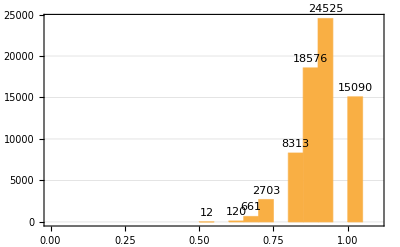

```mathematica
Histogram[journeySat[15,70000, {0.95,0.90, 0.85, 0.95, 0.90, 0.90, 0.90, 0.90, 0.90, 0.90, 0.90, 0.90, 0.90, 0.90, 0.90}], PlotRange-> {{0,1.1}, Automatic}, PlotTheme->"Business", LabelingFunction-> Above, FrameTicks->Table[i,{i,0,1,0.1}], Ticks->Table[i,{i,0,1,0.1}]]
```

```mathematica
cj = journeySat[5, 70000, {0.95,0.90, 0.85, 0.95, 0.90}];
```

```mathematica
cj[[5]]
```

1.

```mathematica
(* Number of journeys with customer satisfaction between 0.9 and 1 *)
Count[cj, x_ /; x > 0.7 && x ≤ 1]
```

65432

```mathematica
custJourneyResults[customerJourneySats_, {rangeLow_, rangeHigh_}]:= Module[{counts, percs},
(* customerJourneySats is the output of the journeySat function *)
(* rangeLow is the low end of the customer sat range specified in the interval rangeLow to rangeHigh *)
(* rangeHigh is the high end of the customer sat range specified in the interval rangeLow to rangeHigh *)
(* outType can be "count" or "perc" *)
counts = Count[customerJourneySats, x_ /; x > rangeLow && x ≤ rangeHigh];
percs = N[counts/Length[customerJourneySats]] * 100;

(* The output consists of two quantities -- the first is the raw count and the second is the percentages of customers with the customer satisfaction ratings. *)
(* {counts, percs}; *)

(* To keep it simple, just output the percentage of customers who have a satisfaction rating greater than rangeLow and less than or equal to rangeHigh *)
percs

];
```

```mathematica
satIntervals = Table[{i, i+0.05}, {i, 0, .95, .05}]
```

{{0.,0.05},{0.05,0.1},{0.1,0.15},{0.15,0.2},{0.2,0.25},{0.25,0.3},{0.3,0.35},{0.35,0.4},{0.4,0.45},{0.45,0.5},{0.5,0.55},{0.55,0.6},{0.6,0.65},{0.65,0.7},{0.7,0.75},{0.75,0.8},{0.8,0.85},{0.85,0.9},{0.9,0.95},{0.95,1.}}

```mathematica
res = custJourneyResults[cj, #] & /@ satIntervals
```

{0.,0.,0.,0.02,0.,0.,0.,0.582857,0.,0.,0.,5.92286,0.,0.,0.,31.5043,0.,0.,0.,61.97}

```mathematica
resPercs = res[[All,2]]
```

Part::partd: Part specification {0.,0.,0.,0.02,0.,0.,0.,0.582857,0.,0.,0.,5.92286,0.,0.,0.,31.5043,0.,0.,0.,61.97}⟦All,2⟧ is longer than depth of object.

{0.,0.,0.,0.02,0.,0.,0.,0.582857,0.,0.,0.,5.92286,0.,0.,0.,31.5043,0.,0.,0.,61.97}⟦All,2⟧

```mathematica
resVals = Transpose[{satIntervals * 100, resPercs}]
```

Transpose::nmtx: The first two levels of {{{0.,5.},{5.,10.},{10.,15.},{15.,20.},{20.,25.},{25.,30.},{30.,35.},{35.,40.},{40.,45.},{45.,50.},{50.,55.},{55.,60.},{60.,65.},{65.,70.},{70.,75.},{75.,80.},{80.,85.},{85.,90.},{90.,95.},{95.,100.}},«1»} cannot be transposed.

Transpose[{{{0.,5.},{5.,10.},{10.,15.},{15.,20.},{20.,25.},{25.,30.},{30.,35.},{35.,40.},{40.,45.},{45.,50.},{50.,55.},{55.,60.},{60.,65.},{65.,70.},{70.,75.},{75.,80.},{80.,85.},{85.,90.},{90.,95.},{95.,100.}},{0.,0.,0.,0.02,0.,0.,0.,0.582857,0.,0.,0.,5.92286,0.,0.,0.,31.5043,0.,0.,0.,61.97}⟦All,2⟧}]

```mathematica
tresVals = Prepend[resVals, {"% Satisfaction Rate\n of Journey", "% Customers"}]
```

Transpose::tperm: Permutation {{{0.,5.},{5.,10.},{10.,15.},{15.,20.},{20.,25.},{25.,30.},{30.,35.},{35.,40.},{40.,45.},{45.,50.},{50.,55.},{55.,60.},{60.,65.},{65.,70.},{70.,75.},{75.,80.},{80.,85.},{85.,90.},{90.,95.},{95.,100.}},«1»} is longer than the dimensions {2} of the expression.

Transpose[{% Satisfaction Rate
 of Journey,% Customers},{{{0.,5.},{5.,10.},{10.,15.},{15.,20.},{20.,25.},{25.,30.},{30.,35.},{35.,40.},{40.,45.},{45.,50.},{50.,55.},{55.,60.},{60.,65.},{65.,70.},{70.,75.},{75.,80.},{80.,85.},{85.,90.},{90.,95.},{95.,100.}},{0.,0.,0.,0.02,0.,0.,0.,0.582857,0.,0.,0.,5.92286,0.,0.,0.,31.5043,0.,0.,0.,61.97}⟦All,2⟧}]

```mathematica
Grid[tresVals, Dividers->All, Alignment->Left]
```

Grid[Transpose[{% Satisfaction Rate
 of Journey,% Customers},{{{0.,5.},{5.,10.},{10.,15.},{15.,20.},{20.,25.},{25.,30.},{30.,35.},{35.,40.},{40.,45.},{45.,50.},{50.,55.},{55.,60.},{60.,65.},{65.,70.},{70.,75.},{75.,80.},{80.,85.},{85.,90.},{90.,95.},{95.,100.}},{0.,0.,0.,0.02,0.,0.,0.,0.582857,0.,0.,0.,5.92286,0.,0.,0.,31.5043,0.,0.,0.,61.97}⟦All,2⟧}],Dividers→All,Alignment→Left]

```mathematica
journeyPerformance[nTouchPoints_, nCustomers_, satisfactionRates_, {rangeLow_, rangeHigh_}]:= Module[{custJourneySatRatios, satPercIntervals, percCustAtSatRange},
(* Use the helper functions journeySat and custJourneyResults *)

(* custJourneySatRatios is the output of journeySat -- it gives the journey satisfaction rate for each customer in nCustomers *)
custJourneySatRatios = journeySat[nTouchPoints, nCustomers, satisfactionRates];

(* use this as an input to custJourneyResults *)
(* percCustAtSatRange gives the percentage of customers whose journeys have a satisfaction rate that is greater than rangeLow and less than or equal to rangeHigh *)
(* Create the customer satisfaction level bins *)
(* satPercIntervals = Table[{i, i+0.05}, {i, 0, .95, .05}]; *)
percCustAtSatRange = custJourneyResults[custJourneySatRatios, {rangeLow, rangeHigh}]
];

satPercIntervals = Table[{i, i+0.05}, {i, 0, .95, .05}]
```

{{0.,0.05},{0.05,0.1},{0.1,0.15},{0.15,0.2},{0.2,0.25},{0.25,0.3},{0.3,0.35},{0.35,0.4},{0.4,0.45},{0.45,0.5},{0.5,0.55},{0.55,0.6},{0.6,0.65},{0.65,0.7},{0.7,0.75},{0.75,0.8},{0.8,0.85},{0.85,0.9},{0.9,0.95},{0.95,1.}}

```mathematica
axisLabels = {"0%-5%", "6%-10%", "11%-15%", "16%-20%", "21%-25%", "26%-30%", "31%-35%", "36%-40%", "41%-45%", "46%-50%", "51%-55%", "56%-60%", "61%-65%", "66%-70%", "71%-75%", "76%-80%", "81%-85%", "86%-90%", "91%-95%", "96%-100%"};
```

```mathematica
tableHeadings = {"Min", "25th Percentile", "Median", "75th Percentile", "Mean", "Max"};
```

## 5 touch points, 100 customers, 95% silo satisfaction rate, 1000 simulations

```mathematica
r1 = Table[journeyPerformance[5, 100, {0.95, 0.95, 0.95, 0.95, 0.95},#], 1000] & /@ satPercIntervals;
```

```mathematica
r1Desc = {Min[#], Max[#]} & /@ r1
```

{{0.,0.},{0.,0.},{0.,0.},{0.,1.},{0.,0.},{0.,0.},{0.,0.},{0.,2.},{0.,0.},{0.,0.},{0.,0.},{0.,9.},{0.,0.},{0.,0.},{0.,0.},{10.,38.},{0.,0.},{0.,0.},{0.,0.},{62.,89.}}

```mathematica
r1Mean = Mean[#] & /@ r1
```

{0.,0.,0.,0.002,0.,0.,0.,0.129,0.,0.,0.,2.124,0.,0.,0.,20.377,0.,0.,0.,77.325}

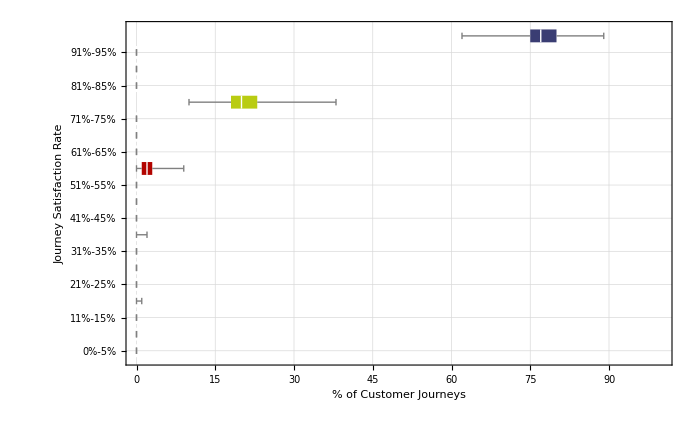

```mathematica
g1 = BoxWhiskerChart[r1, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize->700]
```

## 5 touch points, 1000 customers, 95% silo satisfaction rate, 1000 simulations

```mathematica
r2 = Table[journeyPerformance[5, 1000, {0.95, 0.95, 0.95, 0.95, 0.95},#], 1000] & /@ satPercIntervals;
```

```mathematica
r2Desc = {Min[#], Max[#]} & /@ r2
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.1},{0.,0.},{0.,0.},{0.,0.},{0.,0.6},{0.,0.},{0.,0.},{0.,0.},{0.9,3.8},{0.,0.},{0.,0.},{0.,0.},{15.9,24.5},{0.,0.},{0.,0.},{0.,0.},{73.4,81.6}}

```mathematica
r2Mean = Mean[#] & /@ r2
```

{0.,0.,0.,0.0026,0.,0.,0.,0.112,0.,0.,0.,2.1391,0.,0.,0.,20.3521,0.,0.,0.,77.3337}

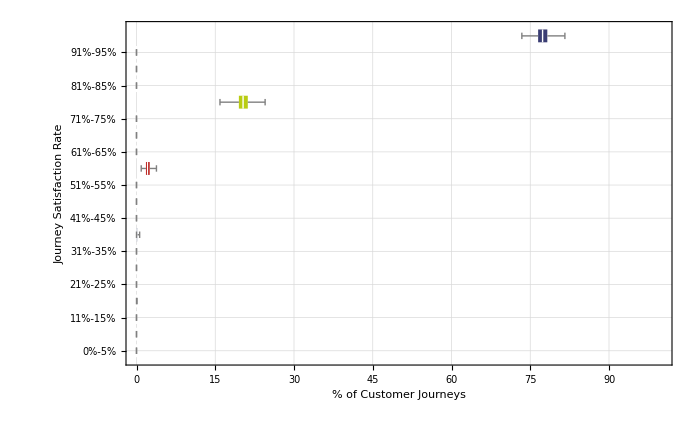

```mathematica
g2 = BoxWhiskerChart[r2, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize->700]
```

```mathematica
r2Table = Flatten[{Min[#], Quartiles[#], Mean[#], Max[#]}] & /@ r2
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0026,0.1},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.1,0.2,0.112,0.6},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.9,1.8,2.1,2.5,2.1391,3.8},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{15.9,19.5,20.3,21.2,20.3521,24.5},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{73.4,76.5,77.35,78.25,77.3337,81.6}}

```mathematica
r2TableDisplay = TableForm[r2Table, TableHeadings->{axisLabels, tableHeadings}]
```

| Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0.0026 | 0.1
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0.1 | 0.2 | 0.112 | 0.6
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0.9 | 1.8 | 2.1 | 2.5 | 2.1391 | 3.8
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0. | 0.
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 15.9 | 19.5 | 20.3 | 21.2 | 20.3521 | 24.5
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 0. | 0. | 0. | 0. | 0. | 0.
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 73.4 | 76.5 | 77.35 | 78.25 | 77.3337 | 81.6

## 10 touch points, 1000 customers, 95% silo satisfaction rate, 1000 simulations

```mathematica
r3 = Table[journeyPerformance[10, 1000, {0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95},#], 1000] & /@ satPercIntervals;
```

```mathematica
r3Mean = Mean[#] & /@ r3
```

{0.,0.,0.,0.,0.,0.,0.,0.0004,0.,0.006,0.,0.0998,0.,1.0617,0.,7.5051,0.,31.5901,0.,59.826}

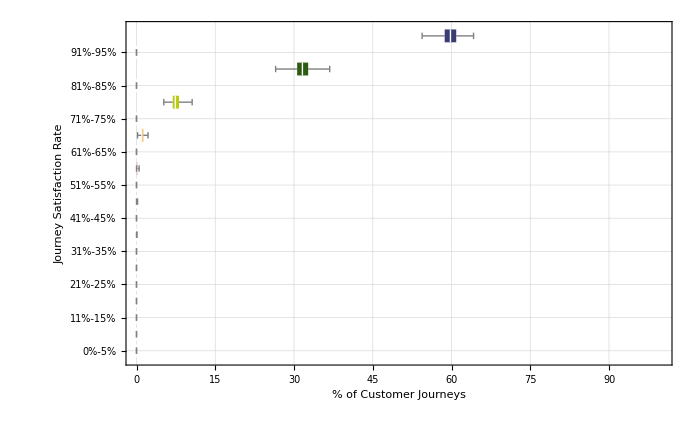

```mathematica
g3 = BoxWhiskerChart[r3, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize -> 700]
```

```mathematica
r3Desc = {Min[#], Max[#]} & /@ r3
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.1},{0.,0.},{0.,0.2},{0.,0.},{0.,0.5},{0.,0.},{0.2,2.2},{0.,0.},{5.2,10.6},{0.,0.},{26.5,36.8},{0.,0.},{54.4,64.2}}

```mathematica
r3Table = Flatten[{Min[#], Quartiles[#], Mean[#], Max[#]}] & /@ r3
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0004,0.1},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.006,0.2},{0.,0.,0.,0.,0.,0.},{0.,0.,0.1,0.2,0.0998,0.5},{0.,0.,0.,0.,0.,0.},{0.2,0.9,1.,1.3,1.0617,2.2},{0.,0.,0.,0.,0.,0.},{5.2,6.9,7.4,8.1,7.5051,10.6},{0.,0.,0.,0.,0.,0.},{26.5,30.6,31.6,32.7,31.5901,36.8},{0.,0.,0.,0.,0.,0.},{54.4,58.7,59.8,60.9,59.826,64.2}}

```mathematica
r3TableDisplay = TableForm[r3Table, TableHeadings->{axisLabels, tableHeadings}]
```

| Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0.0004 | 0.1
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0.006 | 0.2
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0.1 | 0.2 | 0.0998 | 0.5
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0.2 | 0.9 | 1. | 1.3 | 1.0617 | 2.2
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 5.2 | 6.9 | 7.4 | 8.1 | 7.5051 | 10.6
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 26.5 | 30.6 | 31.6 | 32.7 | 31.5901 | 36.8
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 54.4 | 58.7 | 59.8 | 60.9 | 59.826 | 64.2

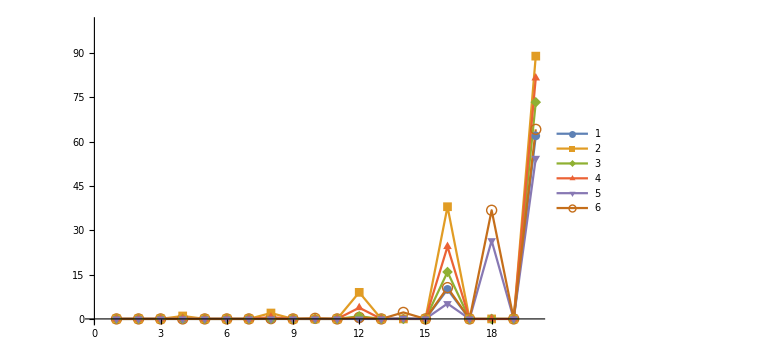

```mathematica
g3List1 = ListLinePlot[{r1Desc[[All,1]], r1Desc[[All,2]],r2Desc[[All,1]], r2Desc[[All,2]],r3Desc[[All,1]], r3Desc[[All,2]]}, PlotRange -> {0,100}, PlotMarkers->Automatic, PlotLegends->Automatic, ImageSize->Large]
```

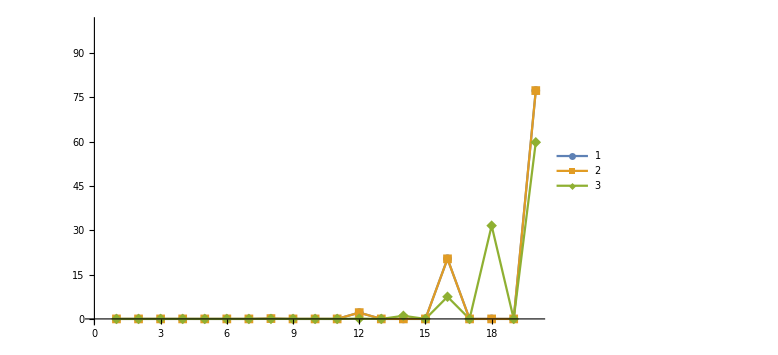

```mathematica
g3List2 = ListLinePlot[{r1Mean, r2Mean, r3Mean}, PlotRange -> {0,100}, PlotMarkers->Automatic, PlotLegends->Automatic, ImageSize->Large]
```

## 15 touch points, 1000 customers, 95% silo satisfaction rate, 1000 simulations

```mathematica
r4 = Table[journeyPerformance[15, 1000, {0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95},#], 1000] & /@ satPercIntervals;
```

```mathematica
r4Mean = Mean[#] & /@ r4
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0002,0.0054,0.,0.0568,0.4896,3.0817,0.,13.4314,36.5839,46.3199}

```mathematica
r4Desc = {Min[#], Max[#]} & /@ r4
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.1},{0.,0.2},{0.,0.},{0.,0.4},{0.,1.5},{1.5,4.9},{0.,0.},{10.7,16.7},{31.7,41.2},{41.,52.2}}

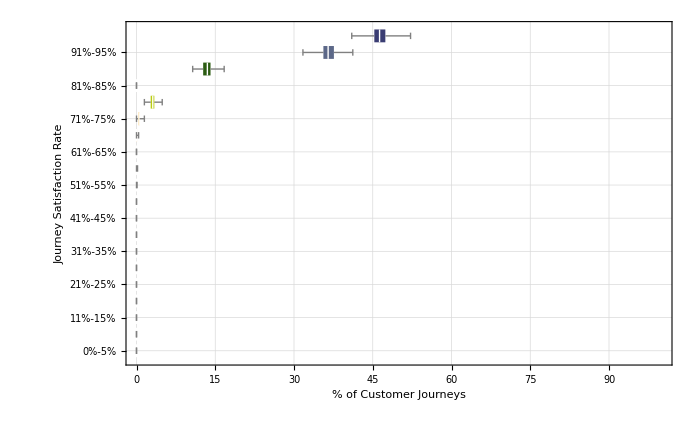

```mathematica
g4 = BoxWhiskerChart[r4, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize->700]
```

```mathematica
r4Table = Flatten[{Min[#], Quartiles[#], Mean[#], Max[#]}] & /@ r4
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0002,0.1},{0.,0.,0.,0.,0.0054,0.2},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.1,0.0568,0.4},{0.,0.3,0.5,0.6,0.4896,1.5},{1.5,2.7,3.1,3.4,3.0817,4.9},{0.,0.,0.,0.,0.,0.},{10.7,12.7,13.5,14.1,13.4314,16.7},{31.7,35.6,36.5,37.6,36.5839,41.2},{41.,45.3,46.3,47.4,46.3199,52.2}}

```mathematica
r4TableDisplay = TableForm[r4Table, TableHeadings->{axisLabels, tableHeadings}]
```

| Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0.0002 | 0.1
56%-60% | 0. | 0. | 0. | 0. | 0.0054 | 0.2
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0.1 | 0.0568 | 0.4
71%-75% | 0. | 0.3 | 0.5 | 0.6 | 0.4896 | 1.5
76%-80% | 1.5 | 2.7 | 3.1 | 3.4 | 3.0817 | 4.9
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 10.7 | 12.7 | 13.5 | 14.1 | 13.4314 | 16.7
91%-95% | 31.7 | 35.6 | 36.5 | 37.6 | 36.5839 | 41.2
96%-100% | 41. | 45.3 | 46.3 | 47.4 | 46.3199 | 52.2

## 20 touch points, 1000 customers, 95% silo satisfaction rate, 1000 simulations

```mathematica
r5 = Table[journeyPerformance[20, 1000, {0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95, 0.95},#], 1000] & /@ satPercIntervals;
```

```mathematica
r5Mean = Mean[#] & /@ r5
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0025,0.0311,0.2201,1.303,5.9605,18.9274,37.7043,35.9764}

```mathematica
r5Desc = {Min[#], Max[#]} & /@ r5
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.1},{0.,0.3},{0.,1.},{0.2,2.5},{3.9,8.3},{15.4,23.3},{32.8,42.2},{32.1,40.8}}

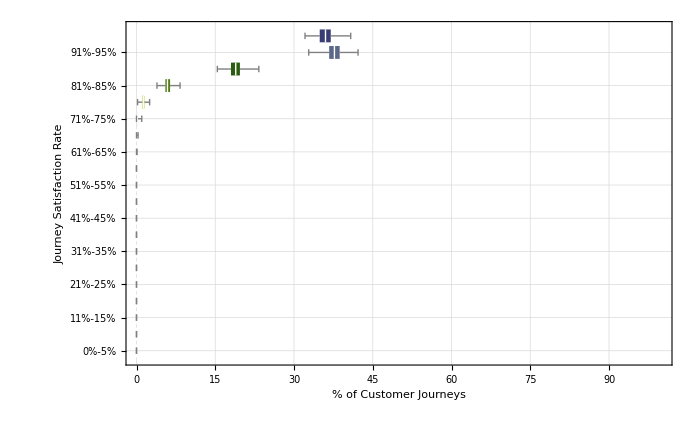

```mathematica
g5 = BoxWhiskerChart[r5, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize->700]
```

```mathematica
r5Table = Flatten[{Min[#], Quartiles[#], Mean[#], Max[#]}] & /@ r5
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0025,0.1},{0.,0.,0.,0.1,0.0311,0.3},{0.,0.1,0.2,0.3,0.2201,1.},{0.2,1.1,1.3,1.5,1.303,2.5},{3.9,5.5,5.9,6.4,5.9605,8.3},{15.4,18.,18.9,19.7,18.9274,23.3},{32.8,36.7,37.7,38.7,37.7043,42.2},{32.1,34.9,36.,37.,35.9764,40.8}}

```mathematica
r5TableDisplay = TableForm[r5Table, TableHeadings->{axisLabels, tableHeadings}]
```

| Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0.0025 | 0.1
66%-70% | 0. | 0. | 0. | 0.1 | 0.0311 | 0.3
71%-75% | 0. | 0.1 | 0.2 | 0.3 | 0.2201 | 1.
76%-80% | 0.2 | 1.1 | 1.3 | 1.5 | 1.303 | 2.5
81%-85% | 3.9 | 5.5 | 5.9 | 6.4 | 5.9605 | 8.3
86%-90% | 15.4 | 18. | 18.9 | 19.7 | 18.9274 | 23.3
91%-95% | 32.8 | 36.7 | 37.7 | 38.7 | 37.7043 | 42.2
96%-100% | 32.1 | 34.9 | 36. | 37. | 35.9764 | 40.8

## 25 touch points, 1000 customers, 95% silo satisfaction rate, 1000 simulations

```mathematica
Table[0.95,25]
```

{0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95}

```mathematica
r6 = Table[journeyPerformance[25, 1000, Table[0.95,25],#], 1000] & /@ satPercIntervals;
```

```mathematica
r6Mean = Mean[#] & /@ r6
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0025,0.0153,0.7099,2.7211,9.298,23.1256,64.2794}

```mathematica
r6Desc = {Min[#], Max[#]} & /@ r6
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.1},{0.,0.2},{0.,1.6},{1.1,4.3},{6.7,12.6},{19.3,26.9},{59.6,69.3}}

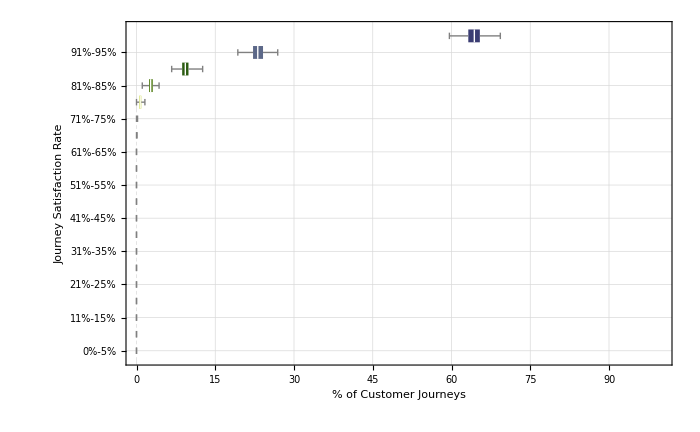

```mathematica
g6 = BoxWhiskerChart[r6, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize->700]
```

```mathematica
r6Table = Flatten[{Min[#], Quartiles[#], Mean[#], Max[#]}] & /@ r6
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0025,0.1},{0.,0.,0.,0.,0.0153,0.2},{0.,0.5,0.7,0.9,0.7099,1.6},{1.1,2.4,2.7,3.1,2.7211,4.3},{6.7,8.7,9.3,9.9,9.298,12.6},{19.3,22.2,23.1,24.1,23.1256,26.9},{59.6,63.2,64.35,65.4,64.2794,69.3}}

```mathematica
r6TableDisplay = TableForm[r6Table, TableHeadings->{axisLabels, tableHeadings}]
```

| Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0.0025 | 0.1
71%-75% | 0. | 0. | 0. | 0. | 0.0153 | 0.2
76%-80% | 0. | 0.5 | 0.7 | 0.9 | 0.7099 | 1.6
81%-85% | 1.1 | 2.4 | 2.7 | 3.1 | 2.7211 | 4.3
86%-90% | 6.7 | 8.7 | 9.3 | 9.9 | 9.298 | 12.6
91%-95% | 19.3 | 22.2 | 23.1 | 24.1 | 23.1256 | 26.9
96%-100% | 59.6 | 63.2 | 64.35 | 65.4 | 64.2794 | 69.3

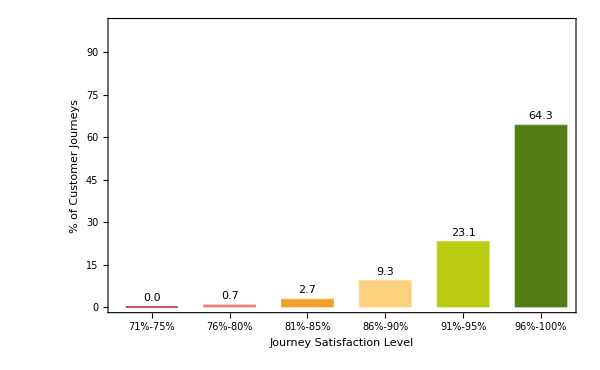
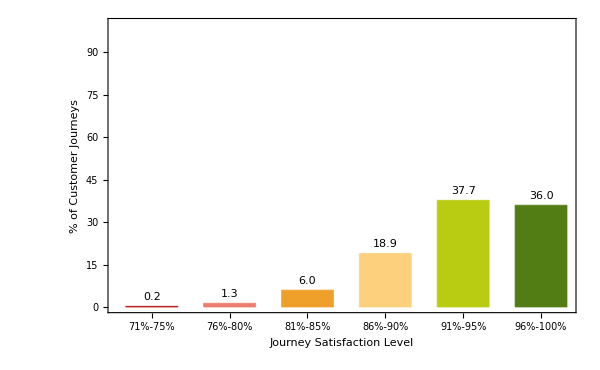
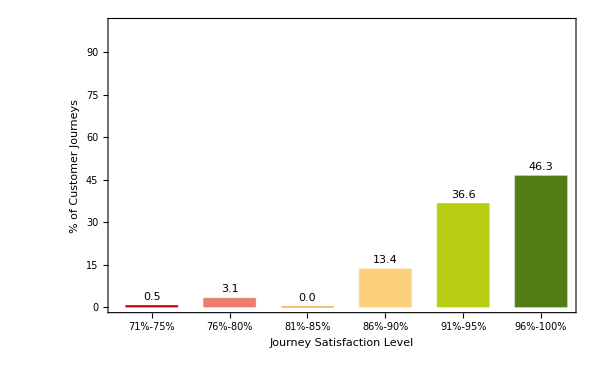
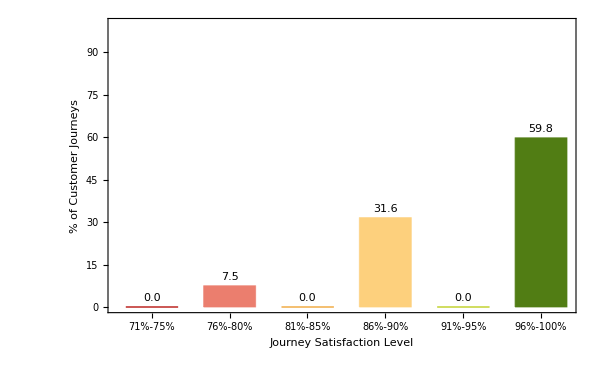
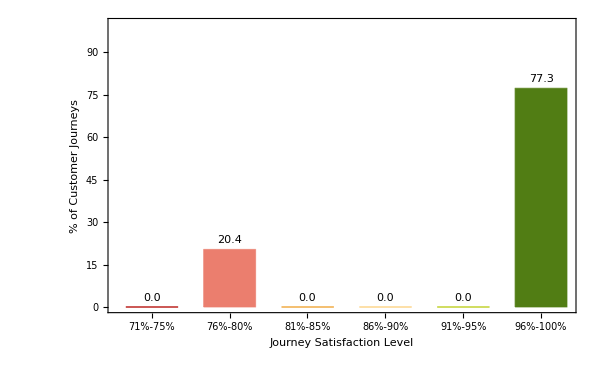

```mathematica
BarChart[#, ChartLabels-> Take[axisLabels,-6], ImageSize->600, BarSpacing->Large, LabelingFunction-> (Placed[NumberForm[#,{3,1}],Above]&), PlotRange-> {0,100}, Frame-> {True,True,False,False}, FrameLabel->{"Journey Satisfaction Level","% of Customer Journeys"},BaseStyle->Directive[Black,Bold,11], LabelStyle->Directive[Black,Bold,12],ChartStyle->10] & /@ {Take[r6Mean,-6], Take[r5Mean,-6], Take[r4Mean,-6], Take[r3Mean,-6], Take[r2Mean,-6]}
```

This is a really funky pattern! One thing is for sure -- the percentage of customer journeys that have a 95% or above satisfaction level is ALWAYS well under 95%!

## Build the output function

```mathematica
journeyOutput[nTouchPoints_, nCustomers_, siloSatisfactionRates_, journeySatIntervals_, outputType_:"mean"]:= Module[{nSimulations = 200,simResults, simStats, axisLabels, tableHeadings, simStatsTable, bwChart, barMean},
(* outputType can be "mean" (default), "raw", "table", "boxWhisker" *)

If[nTouchPoints ≠ Length[siloSatisfactionRates], Return["Number of touchpoints should be the same as the number of silo satisfaction rates. Please correct this and try again."]];

(* Get the results for all the intervals of journey satisfaction level -- can be the full range from 0% to 100% as in satPerIntervals or can be a subset of that *)
simResults = Table[journeyPerformance[nTouchPoints, nCustomers, siloSatisfactionRates,#], nSimulations] & /@ journeySatIntervals;
simStats = Flatten[{Min[#], Quartiles[#], Mean[#], Max[#]}] & /@ simResults;

(* Build the table of simStats *)
axisLabels = {"0%-5%", "6%-10%", "11%-15%", "16%-20%", "21%-25%", "26%-30%", "31%-35%", "36%-40%", "41%-45%", "46%-50%", "51%-55%", "56%-60%", "61%-65%", "66%-70%", "71%-75%", "76%-80%", "81%-85%", "86%-90%", "91%-95%", "96%-100%"};
tableHeadings = {"Min", "25th Percentile", "Median", "75th Percentile", "Mean", "Max"};
simStatsTable = TableForm[simStats, TableHeadings->{axisLabels, tableHeadings}];

(* Build the box whisker plot *)
bwChart = BoxWhiskerChart[simResults, ChartLabels -> axisLabels, BarOrigin->Left, GridLines -> Automatic, FrameLabel -> {"% of Customer Journeys", "Journey Satisfaction Rate"}, PlotRange -> {{0,100},All}, ChartStyle->10, ImageSize->700, PlotLabel->"Test"];

(* Build the bar graph output for the means *)
(* To keep the display manageable, show only the last 12 journey satisfaction levels -- starting at 41% and ending at 100% *)
barMean = BarChart[Take[simStats[[All,5]],-12], ChartLabels -> Take[axisLabels,-12], ImageSize->700, BarSpacing->Large, LabelingFunction-> (Placed[Round[#],Above]&), PlotRange-> {0,100}, Frame-> {True,True,False,False}, FrameLabel->{"Baseline Journey Satisfaction Rate","Mean % of Customer Journeys"},BaseStyle->Directive[Black,Bold,11], LabelStyle->Directive[Black,Bold,10],ChartStyle->24, PlotLabel-> ToString[nTouchPoints] <> " Touchpoints" ];

(* Set up the output *)
Switch[outputType, "mean", barMean,"raw", simResults, "table", simStatsTable, "boxWhisker", bwChart, __, simStatsTable]
];
```

```mathematica
satPercIntervals
```

{{0.,0.05},{0.05,0.1},{0.1,0.15},{0.15,0.2},{0.2,0.25},{0.25,0.3},{0.3,0.35},{0.35,0.4},{0.4,0.45},{0.45,0.5},{0.5,0.55},{0.55,0.6},{0.6,0.65},{0.65,0.7},{0.7,0.75},{0.75,0.8},{0.8,0.85},{0.85,0.9},{0.9,0.95},{0.95,1.}}

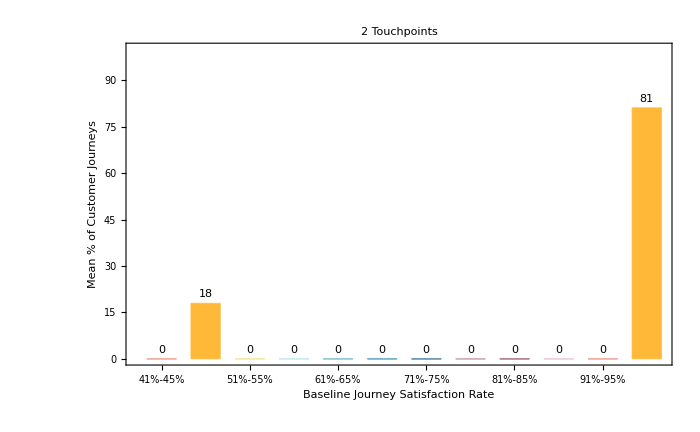
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 14.7 | 17.15 | 18. | 18.8 | 17.9335 | 21.3
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0. | 0.
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 0. | 0. | 0. | 0. | 0. | 0.
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 0. | 0. | 0. | 0. | 0. | 0.
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 76.9 | 80.3 | 80.9 | 81.6 | 80.829 | 83.9,-Graphics-}

```mathematica
j2 = journeyOutput[2,1000, Table[0.9,2],satPercIntervals, #] &/@ {"table", "mean"}
```

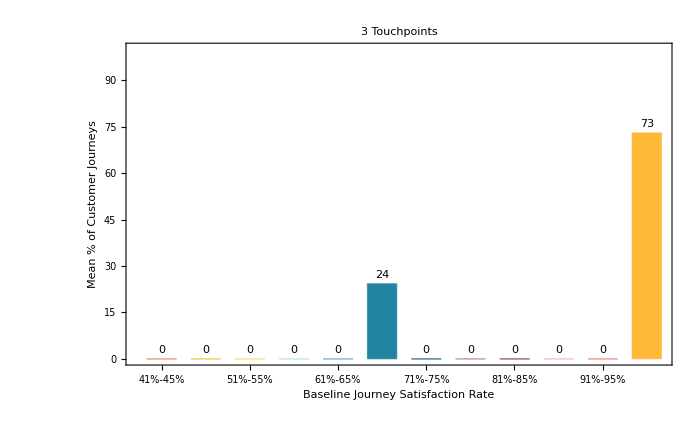
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 1.4 | 2.4 | 2.6 | 2.9 | 2.671 | 4.4
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 20. | 23.45 | 24.3 | 25. | 24.2355 | 28.2
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 0. | 0. | 0. | 0. | 0. | 0.
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 0. | 0. | 0. | 0. | 0. | 0.
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 68.6 | 72.1 | 73.1 | 74. | 73.0425 | 76.5,-Graphics-}

```mathematica
j3 = journeyOutput[3,1000, Table[0.9,3],satPercIntervals, #] &/@ {"table", "mean"}
```

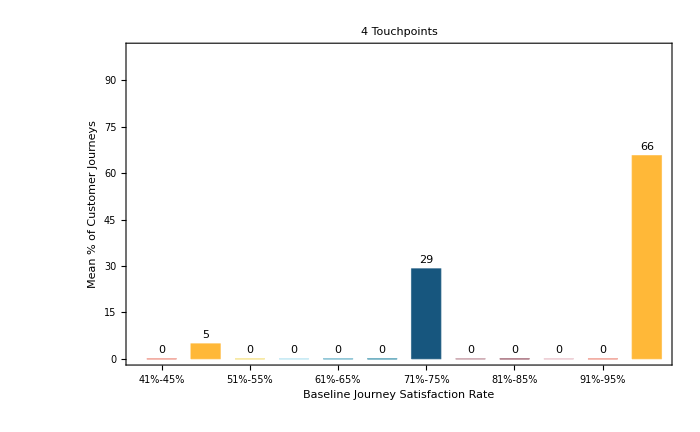
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0.2 | 0.3 | 0.5 | 0.3535 | 0.9
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 3.3 | 4.4 | 4.9 | 5.4 | 4.9035 | 7.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0. | 0.
71%-75% | 25.3 | 28. | 29. | 30. | 29.0335 | 32.7
76%-80% | 0. | 0. | 0. | 0. | 0. | 0.
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 0. | 0. | 0. | 0. | 0. | 0.
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 62. | 64.6 | 65.55 | 66.4 | 65.509 | 69.7,-Graphics-}

```mathematica
j4 = journeyOutput[4,1000, Table[0.9,4],satPercIntervals, #] &/@ {"table", "mean"}
```

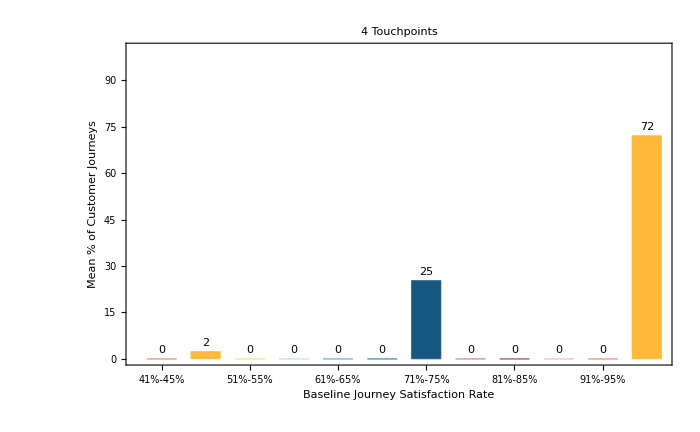
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0.1 | 0.06 | 0.4
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0.9 | 1.7 | 2. | 2.3 | 1.993 | 3.3
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0. | 0.
71%-75% | 16.8 | 20.3 | 21. | 22. | 21.0615 | 24.5
76%-80% | 0. | 0. | 0. | 0. | 0. | 0.
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 0. | 0. | 0. | 0. | 0. | 0.
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 73.3 | 76.1 | 76.9 | 77.95 | 76.9695 | 80.4,-Graphics-}

```mathematica
j4R = journeyOutput[4,1000, RandomReal[{0.8,1.},4],satPercIntervals, #] &/@ {"table", "mean"}
```

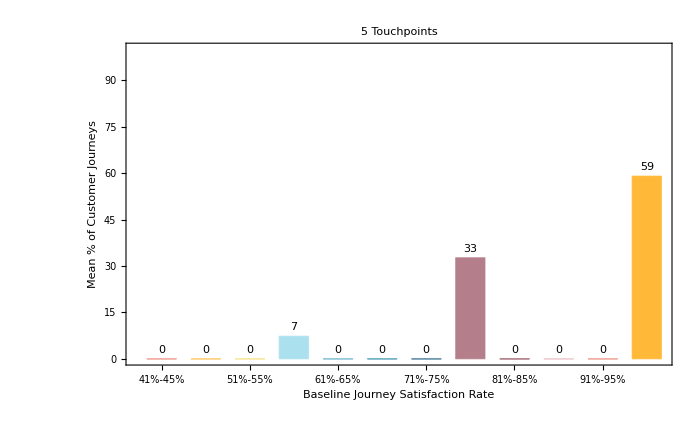
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0.1 | 0.042 | 0.3
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0.2 | 0.6 | 0.8 | 1. | 0.8105 | 1.6
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 5.1 | 6.8 | 7.2 | 7.8 | 7.2805 | 10.6
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0. | 0.
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 29.5 | 31.8 | 32.75 | 33.75 | 32.7935 | 36.4
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 0. | 0. | 0. | 0. | 0. | 0.
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 54.5 | 57.8 | 58.9 | 60.4 | 59.042 | 62.4,-Graphics-}

```mathematica
j5 = journeyOutput[5,1000, Table[0.9,5],satPercIntervals, #] &/@ {"table", "mean"}
```

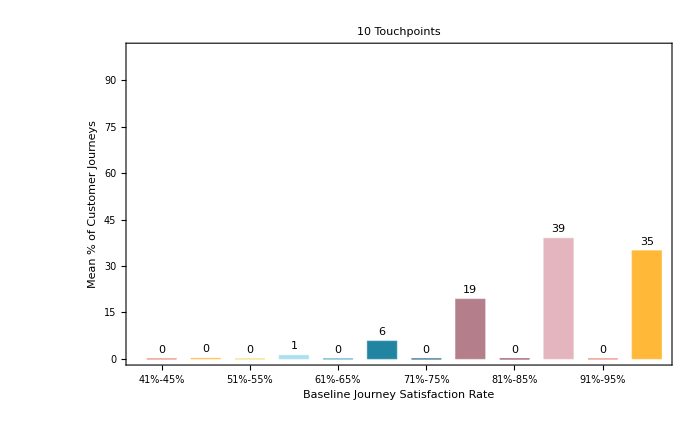
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0.001 | 0.1
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0.012 | 0.2
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0.1 | 0.1 | 0.2 | 0.145 | 0.6
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0.2 | 0.9 | 1.1 | 1.3 | 1.1085 | 2.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 4.2 | 5.2 | 5.7 | 6.3 | 5.731 | 7.6
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 16.1 | 18.5 | 19.4 | 20.2 | 19.3945 | 23.4
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 34.7 | 37.6 | 38.7 | 39.75 | 38.7515 | 45.2
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 31.2 | 34. | 34.9 | 36. | 34.88 | 40.2,-Graphics-}

```mathematica
j10 = journeyOutput[10,1000, Table[0.9,10],satPercIntervals, #] &/@ {"table", "mean"}
```

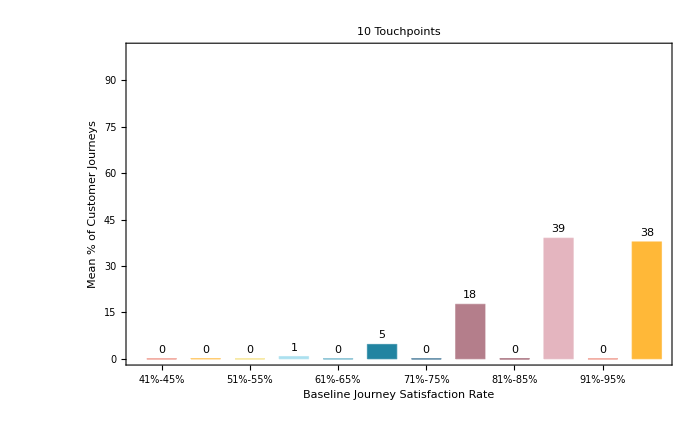
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0.002 | 0.1
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0.1 | 0.046 | 0.3
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0.4 | 0.5 | 0.7 | 0.529 | 1.2
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 2.1 | 3.4 | 3.8 | 4.2 | 3.7675 | 5.2
71%-75% | 0. | 0. | 0. | 0. | 0. | 0.
76%-80% | 13.7 | 15.7 | 16.5 | 17.2 | 16.5045 | 19.9
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 35.7 | 37.95 | 39.3 | 40.35 | 39.247 | 43.3
91%-95% | 0. | 0. | 0. | 0. | 0. | 0.
96%-100% | 34.6 | 38.9 | 39.8 | 40.9 | 39.7795 | 43.2,-Graphics-}

```mathematica
j10R = journeyOutput[10,1000, RandomReal[{0.8,1.},10],satPercIntervals, #] &/@ {"table", "mean"}
```

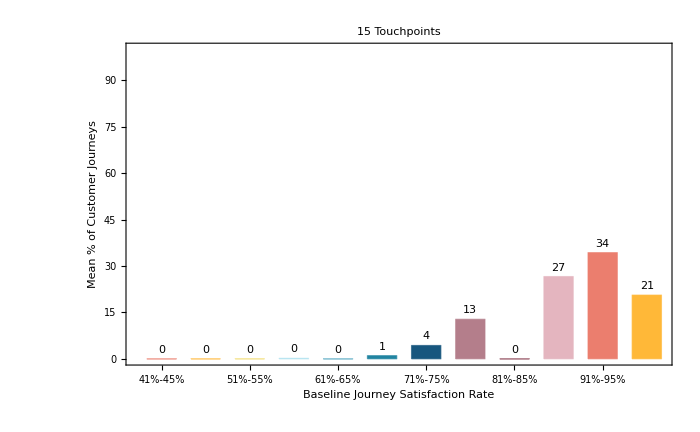
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0.0005 | 0.1
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0.0035 | 0.1
51%-55% | 0. | 0. | 0. | 0.1 | 0.0305 | 0.3
56%-60% | 0. | 0.1 | 0.2 | 0.3 | 0.19 | 0.6
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0.1 | 0.8 | 1. | 1.2 | 1.038 | 2.2
71%-75% | 2.6 | 3.8 | 4.3 | 4.7 | 4.2895 | 6.2
76%-80% | 10. | 12. | 12.7 | 13.35 | 12.7625 | 15.2
81%-85% | 0. | 0. | 0. | 0. | 0. | 0.
86%-90% | 23.1 | 25.8 | 26.7 | 27.85 | 26.7615 | 32.5
91%-95% | 30.4 | 33.35 | 34.3 | 35.3 | 34.351 | 38.1
96%-100% | 17.5 | 19.7 | 20.6 | 21.4 | 20.6075 | 24.9,-Graphics-}

```mathematica
j15 = journeyOutput[15,1000, Table[0.9,15],satPercIntervals, #] &/@ {"table", "mean"}
```

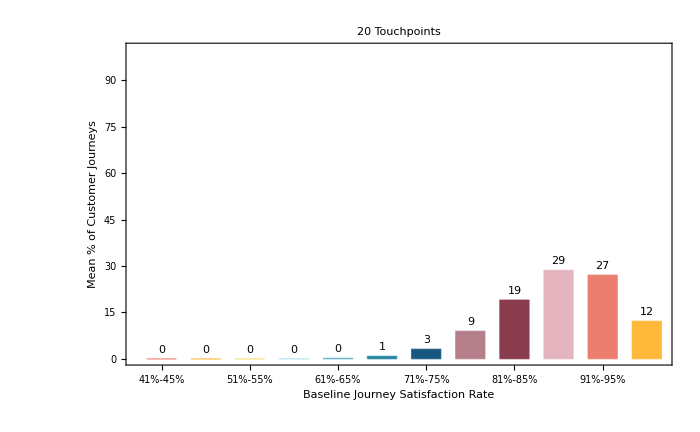
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0.0005 | 0.1
51%-55% | 0. | 0. | 0. | 0. | 0.005 | 0.1
56%-60% | 0. | 0. | 0. | 0.1 | 0.042 | 0.2
61%-65% | 0. | 0.1 | 0.2 | 0.3 | 0.199 | 0.8
66%-70% | 0.2 | 0.7 | 0.9 | 1.1 | 0.906 | 1.8
71%-75% | 1.6 | 2.9 | 3.2 | 3.6 | 3.201 | 4.9
76%-80% | 6.5 | 8.4 | 9. | 9.6 | 9.013 | 11.7
81%-85% | 15.4 | 18. | 19. | 19.8 | 18.8525 | 21.8
86%-90% | 24.7 | 27.6 | 28.4 | 29.4 | 28.4005 | 32.4
91%-95% | 23. | 26. | 26.9 | 27.8 | 26.99 | 30.8
96%-100% | 8.8 | 11.4 | 12.2 | 12.8 | 12.146 | 14.4,-Graphics-}

```mathematica
j20 = journeyOutput[20,1000, Table[0.9,20],satPercIntervals, #] &/@ {"table", "mean"}
```

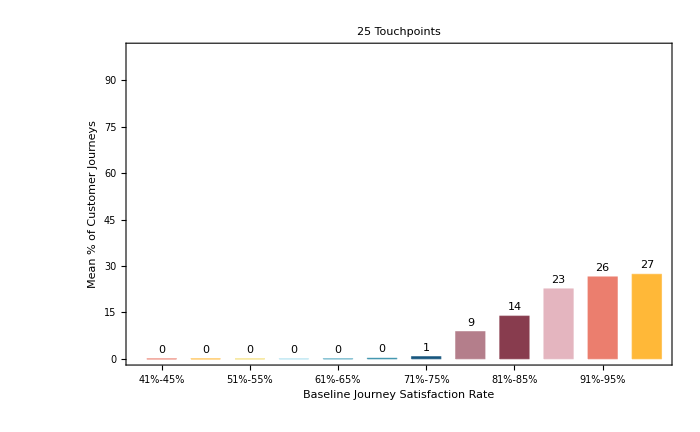
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0.008 | 0.1
61%-65% | 0. | 0. | 0. | 0.1 | 0.0365 | 0.3
66%-70% | 0. | 0.1 | 0.1 | 0.2 | 0.155 | 0.7
71%-75% | 0.1 | 0.5 | 0.7 | 0.9 | 0.728 | 1.8
76%-80% | 6.6 | 8.3 | 8.9 | 9.4 | 8.8605 | 10.9
81%-85% | 10.8 | 13.2 | 13.8 | 14.6 | 13.8825 | 16.9
86%-90% | 20.3 | 21.8 | 22.6 | 23.45 | 22.612 | 26.6
91%-95% | 23.2 | 25.9 | 26.6 | 27.3 | 26.5525 | 30.1
96%-100% | 23.8 | 25.9 | 27. | 28. | 26.966 | 31.,-Graphics-}

```mathematica
j25 = journeyOutput[25,1000, Table[0.9,25],satPercIntervals, #] &/@ {"table", "mean"}
```

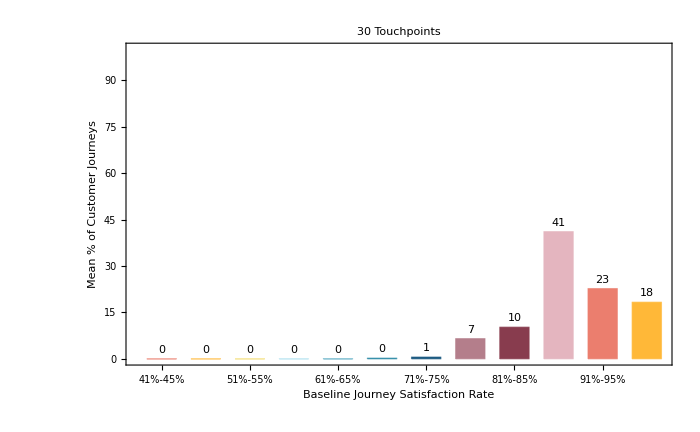
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0.0025 | 0.1
61%-65% | 0. | 0. | 0. | 0. | 0.006 | 0.1
66%-70% | 0. | 0.1 | 0.2 | 0.3 | 0.183 | 0.6
71%-75% | 0. | 0.4 | 0.5 | 0.7 | 0.559 | 1.3
76%-80% | 4.9 | 6.2 | 6.6 | 7.1 | 6.6385 | 8.6
81%-85% | 7.5 | 9.5 | 10.15 | 10.7 | 10.138 | 12.8
86%-90% | 36.9 | 40. | 41.1 | 42.2 | 41.1585 | 44.8
91%-95% | 18.4 | 22. | 22.7 | 23.7 | 22.759 | 26.3
96%-100% | 15.6 | 17.4 | 18.3 | 19. | 18.2545 | 22.2,-Graphics-}

```mathematica
j30 = journeyOutput[30,1000, Table[0.9,30],satPercIntervals, #] &/@ {"table", "mean"}
```

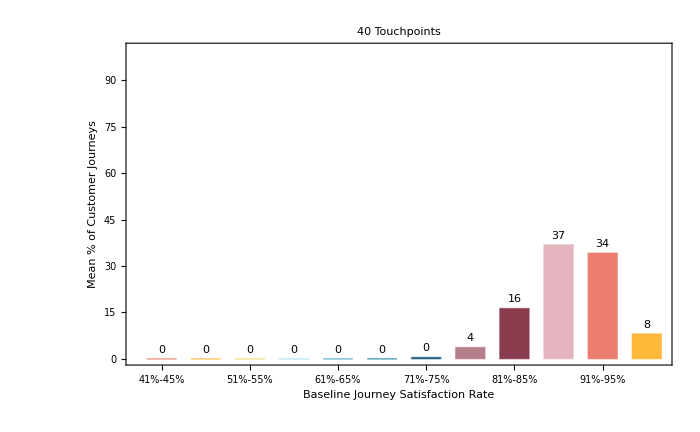
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0.001 | 0.1
66%-70% | 0. | 0. | 0. | 0.1 | 0.0405 | 0.3
71%-75% | 0. | 0.3 | 0.4 | 0.6 | 0.461 | 1.2
76%-80% | 2.1 | 3.3 | 3.7 | 4.05 | 3.689 | 5.2
81%-85% | 12. | 15.7 | 16.5 | 17.45 | 16.522 | 19.3
86%-90% | 33.3 | 36.1 | 37. | 38.2 | 37.123 | 41.8
91%-95% | 30.1 | 33.05 | 34.1 | 35.2 | 34.0995 | 37.2
96%-100% | 5.8 | 7.55 | 8.15 | 8.65 | 8.134 | 10.4,-Graphics-}

```mathematica
j40 = journeyOutput[40,1000, Table[0.9,40],satPercIntervals, #] &/@ {"table", "mean"}
```

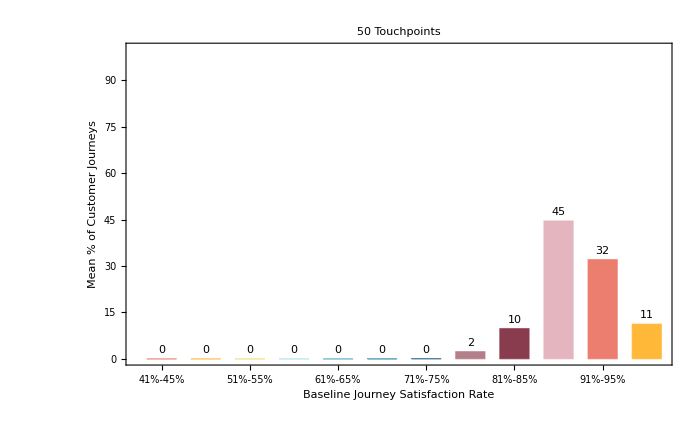
{ | Min | 25th Percentile | Median | 75th Percentile | Mean | Max
0%-5% | 0. | 0. | 0. | 0. | 0. | 0.
6%-10% | 0. | 0. | 0. | 0. | 0. | 0.
11%-15% | 0. | 0. | 0. | 0. | 0. | 0.
16%-20% | 0. | 0. | 0. | 0. | 0. | 0.
21%-25% | 0. | 0. | 0. | 0. | 0. | 0.
26%-30% | 0. | 0. | 0. | 0. | 0. | 0.
31%-35% | 0. | 0. | 0. | 0. | 0. | 0.
36%-40% | 0. | 0. | 0. | 0. | 0. | 0.
41%-45% | 0. | 0. | 0. | 0. | 0. | 0.
46%-50% | 0. | 0. | 0. | 0. | 0. | 0.
51%-55% | 0. | 0. | 0. | 0. | 0. | 0.
56%-60% | 0. | 0. | 0. | 0. | 0. | 0.
61%-65% | 0. | 0. | 0. | 0. | 0. | 0.
66%-70% | 0. | 0. | 0. | 0. | 0.01 | 0.2
71%-75% | 0. | 0. | 0.1 | 0.2 | 0.103 | 0.7
76%-80% | 1.4 | 2.1 | 2.4 | 2.7 | 2.3885 | 3.7
81%-85% | 7.3 | 9. | 9.8 | 10.3 | 9.7775 | 11.7
86%-90% | 39.5 | 43.8 | 44.9 | 46. | 44.8645 | 48.9
91%-95% | 28.6 | 31.05 | 31.8 | 32.75 | 31.9365 | 36.3
96%-100% | 8.7 | 10.5 | 11.1 | 11.7 | 11.0975 | 13.4,-Graphics-}

```mathematica
j50 = journeyOutput[50,1000, Table[0.9,50],satPercIntervals, #] &/@ {"table", "mean"}
```

## Summary of Results

```mathematica
numTouchPoints = {2,3,4,5,10,15,20,25,30,40,50};
selJourneySatRates = { "46%-50%", "51%-55%", "56%-60%", "61%-65%", "66%-70%", "71%-75%", "76%-80%", "81%-85%", "86%-90%", "91%-95%", "96%-100%"};
```

```mathematica
meanPercCustJourneys= {{18,0,0,0,0,0,0,0,0,0,81}, {0,0,0,0,24,0,0,0,0,0,73}, {5,0,0,0,0,29,0,0,0,0,65}, {0,0,7,0,0,0,33,0,0,0,59},{0,0,1,0,6,0,19,0,39,0,35}, {0,0,0,0,1,4,13,0,27,34,21}, {0,0,0,0,1,3,9,19,28,27,12},{0,0,0,0,0,1,9,14,23,27,27}, {0,0,0,0,0,1,7,10,41,23,18}, {0,0,0,0,0,0,4,16,37,34,8}, {0,0,0,0,0,0,2,10,45,32,11}};
```

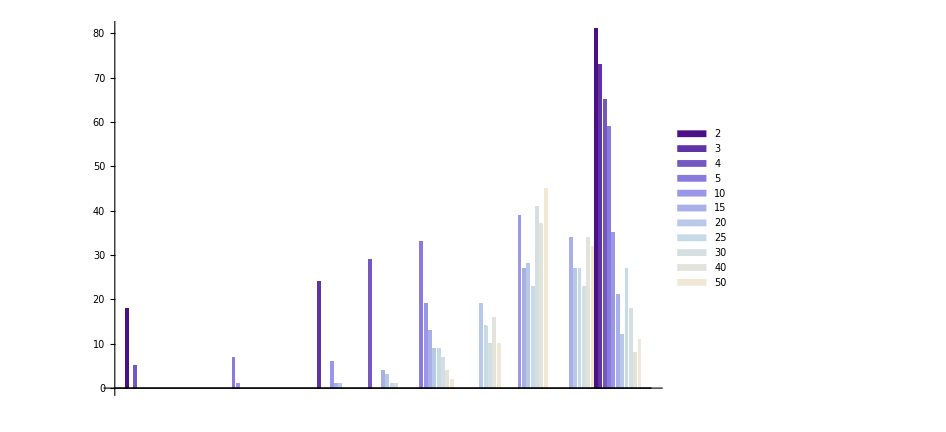

```mathematica
BarChart[Transpose[meanPercCustJourneys], ImageSize->700, ChartLegends->numTouchPoints, BarSpacing->Large, ChartStyle->"LakeColors"]
```

```mathematica
tickMarks = Table[{i, Pane[selJourneySatRates[[i]],80, Alignment -> Center]}, {i, 1, Length[selJourneySatRates]}]
```

{{1,46%-50%},{2,51%-55%},{3,56%-60%},{4,61%-65%},{5,66%-70%},{6,71%-75%},{7,76%-80%},{8,81%-85%},{9,86%-90%},{10,91%-95%},{11,96%-100%}}

```mathematica
ytickMarks = Table[{i, Pane[numTouchPoints[[i]],80, Alignment -> Center]}, {i, 1, Length[numTouchPoints]}]
```

{{1,2},{2,3},{3,4},{4,5},{5,10},{6,15},{7,20},{8,25},{9,30},{10,40},{11,50}}

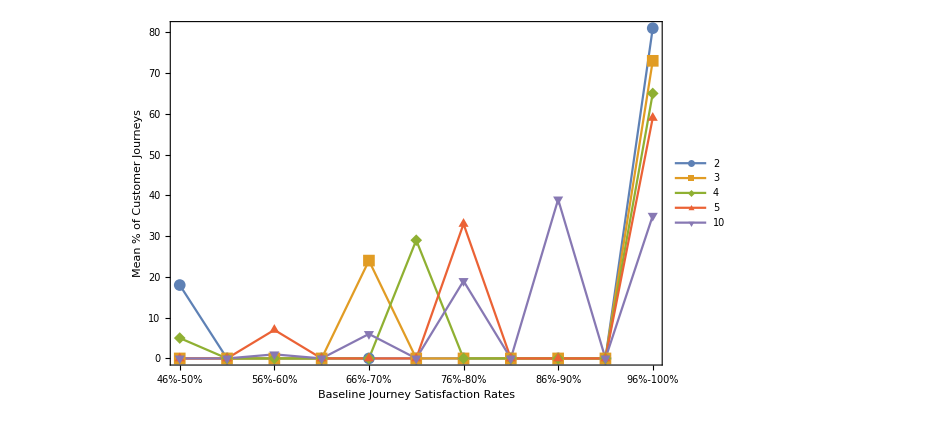

```mathematica
ListLinePlot[Take[meanPercCustJourneys,5], PlotRange->All, PlotMarkers->{Automatic,12}, PlotLegends->Take[numTouchPoints,5], ImageSize->700, Frame -> {True, True,False,False}, FrameLabel->{"Baseline Journey Satisfaction Rates", "Mean % of Customer Journeys"}, FrameTicks -> {tickMarks, Automatic}]
```

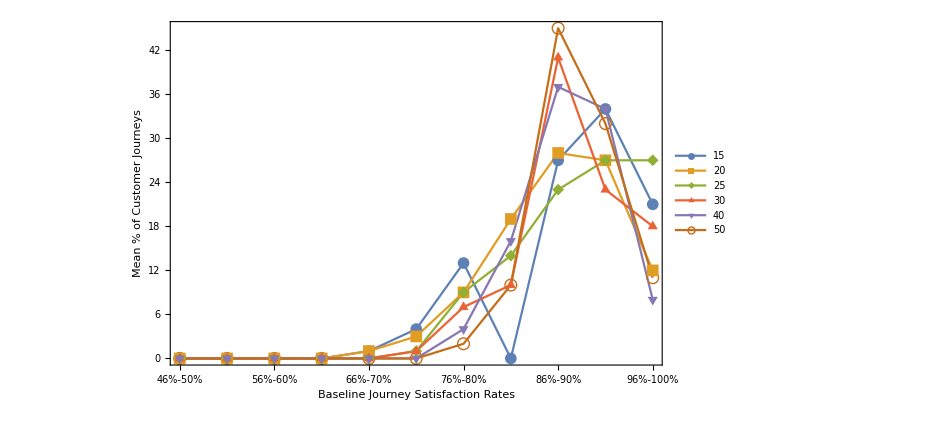

```mathematica
ListLinePlot[Take[meanPercCustJourneys,-6], PlotRange->All, PlotMarkers->{Automatic,12}, PlotLegends->Take[numTouchPoints,-6], ImageSize->700, Frame -> {True, True,False,False}, FrameLabel->{"Baseline Journey Satisfaction Rates", "Mean % of Customer Journeys"}, FrameTicks -> {tickMarks, Automatic}]
```

```mathematica
numTouchPoints
```

{2,3,4,5,10,15,20,25,30,40,50}

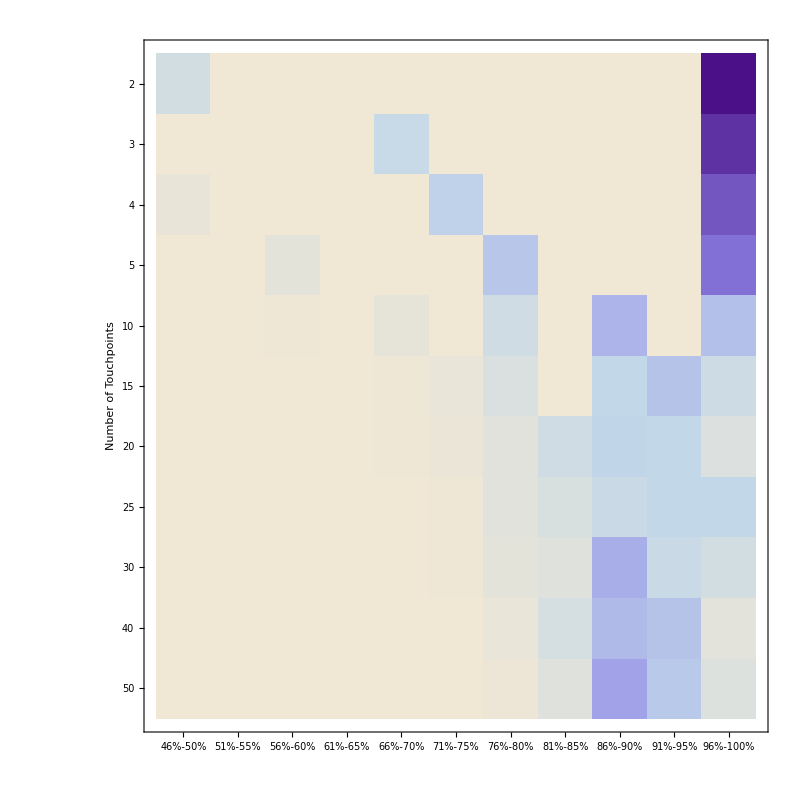

```mathematica
ArrayPlot[meanPercCustJourneys, ColorFunction->ColorData[{"LakeColors","Reverse"}],Frame-> True, FrameLabel-> {"Number of Touchpoints", None, None,"Baseline Journey Satisfaction Rate"}, ImageSize->800, LabelStyle->Directive[Black,Bold,11], FrameTicks -> {ytickMarks,tickMarks,ytickMarks,tickMarks}]
```

```mathematica
TableForm[meanPercCustJourneys, TableHeadings->{numTouchPoints, selJourneySatRates}]
```

| 46%-50% | 51%-55% | 56%-60% | 61%-65% | 66%-70% | 71%-75% | 76%-80% | 81%-85% | 86%-90% | 91%-95% | 96%-100%
2 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81
3 | 0 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 73
4 | 5 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 65
5 | 0 | 0 | 7 | 0 | 0 | 0 | 33 | 0 | 0 | 0 | 59
10 | 0 | 0 | 1 | 0 | 6 | 0 | 19 | 0 | 39 | 0 | 35
15 | 0 | 0 | 0 | 0 | 1 | 4 | 13 | 0 | 27 | 34 | 21
20 | 0 | 0 | 0 | 0 | 1 | 3 | 9 | 19 | 28 | 27 | 12
25 | 0 | 0 | 0 | 0 | 0 | 1 | 9 | 14 | 23 | 27 | 27
30 | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 10 | 41 | 23 | 18
40 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 16 | 37 | 34 | 8
50 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 10 | 45 | 32 | 11

```mathematica
1/(18/100.)
```

5.55556